# CCBH delay time using Ghodla 2023 relation

Davi  C. Rodrigues (this code). Sep, 2023.

```mathematica
ResourceFunction["DarkMode"][]
```

CCBH = Cosmologically coupled black hole (general case)
DEBH = Dark energy coupled Black Hole (implies k = - 3w)
GBH = Growing BH, k is arbitrary and without direct dark energy impact.
m1 = primary (larger) mass of the BBH or NSBH pair.


Naming conventions:
All defined variables/functions start with lower case letter.
“I" at the end of a function name: interpolated version. 
"Raw”: a function without options. It is useful to store results. The version with options is based on the raw version.

## Starting...

```mathematica
SetDirectory[NotebookDirectory[]];
Get[FileNameJoin[{"codes", "Directories.wl"}]];

(*
  Calling wl files
  ***************** 
*)
getCode["Constants.wl"];
baseSimPoints = 10^7; (*The base number of points to be simmulated for each dimension, commonly 10^5-10^7, depends on the purpose.*)

getCode["ObsDataPreparationGWTC-3.wl"]; 
getCode["PowerLawPlusPeakDefinition.wl"];
getCode["Cosmology.wl"];

Print[Style["End of running wl files.", FontColor->LightGray]];

(*
  GENERAL PURPOSE FUNCTIONS
  **************************
*)

sigmaProb::usage = "sigmaProb[probability] yields the number of σ's for a given probability.";
sigmaProb[prob_] := Block[{sigma}, 
  sigma /. FindRoot[NProbability[Abs[x] > sigma , x\[Distributed]NormalDistribution[]] == prob, {sigma, 2}]
];

Clear[probSigma];
probSigma[n_] := probSigma[n] = NProbability[Abs[x] > n, x\[Distributed]NormalDistribution[]];
```

Starting Constants.wl:

Starting ObsDataPreparationGWTC-3.wl:

Number of m1 black holes:   72

Starting PowerLawPlusPeakDefinition.wl:

Use plpp`pi[m, options] for the power-law-plus-peak PDF and plpp`𝒟[options] for the distribution. Use optionsPlpp to see the options.

Starting Cosmology.wl:

tableZformation loaded.

End of running wl files.

## Finding the td distribution for given zObs

```mathematica
zTime[t_?NumberQ] := zTime[t, -1];
timeZ[z_?NumberQ] := timeZ[z, -1];

listZtime0 = ParallelTable[{t, zTime[t]}, {t, 0.0001, 0.0090, 0.0001}]; (* t = 0 is needed to compute zTimeI[timeZ[zObs] - tdC] *)
listZtime1 = ParallelTable[{t, zTime[t]}, {t, 0.010, timeZ[-0.9], 0.01}]; (* t = 0 is needed to compute zTimeI[timeZ[zObs] - tdC] *)

Clear[zTimeI]
listZtime = Join[listZtime0, listZtime1];
zTimeI = Interpolation[listZtime, InterpolationOrder->3];
timeMax = listZtime[[-1,1]]; (*Maximum time used to define zTimeI.*)

Clear[tdKerrF];
SetAttributes[tdKerrF, NumericFunction];

tdKerrF::usage = "tdKerrF[zObs, tdC, k] yields the delay time in the Kerr frame for a BBH that merged at zObs,
and had a tdC delay time wihtin CCBH. tdKerrF is the same of tdKerr, but the latter depends on zi in place of zObs." ;
tdKerrF[zObs_?NumberQ, tdC_?NumberQ, k_?NumberQ]:= Block[{zi},
  zi = zTimeI[timeZ[zObs] - tdC];
  NIntegrate[
    ((1 + zi)/(1 + zTimeI[t]))^(15 k) , 
    {t, timeZ[zObs] - tdC, timeZ[zObs]},
    PrecisionGoal -> 4,
    AccuracyGoal->Infinity
  ]
];
```

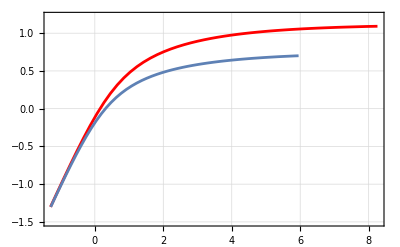

```mathematica
Clear[minLogtdC, maxLogtdC];
{minLogtdC, maxLogtdC[zObs_]} = {Log10[tdmin0], Log10[timeZ[zObs] - timeZ[10]]};

listLogtdKerr35 = ParallelTable[
  {{zObs, logtdC}, Log10@tdKerrF[zObs, 10^logtdC, 3/5]}, 
  {zObs, {0.01, 0.1, 0.4, 0.7, 1.0}},
  {logtdC, minLogtdC, maxLogtdC[zObs], 0.01}
] ~ Flatten ~ 1;

Clear[tdKerr35I, tdKerr3I];
logtdKerr35I = Interpolation[listLogtdKerr35, InterpolationOrder->1];

listLogtdCCBH35 = {{#1[[1]], #2}, #1[[2]]} & @@@ listLogtdKerr35 ; (*Generates a table for the inverse function by flipping table entries. *)
logtdCCBH35I = Interpolation[listLogtdCCBH35, InterpolationOrder-> 1 (*Required*)];
{minLogtdK35[zObs_], maxLogtdK35[zObs_]} := {logtdKerr35I[zObs, minLogtdC], logtdKerr35I[zObs, maxLogtdC[zObs] - 0.01]};

Clear[plottdKtdC, plottdKtdC35];

plottdKtdC35[zObs_, style_:Automatic] := Plot[
  logtdCCBH35I[zObs, logtdK], 
  {logtdK, minLogtdK35[zObs], maxLogtdK35[zObs]},
  PlotRange->{All, {-1.5, Log10[timeZ[0]] + 0.1}},
  GridLines -> Automatic,
  Frame->True,
  Axes->False,
  Background->White,
  FrameStyle->Directive[Black,14, FontFamily-> "Times"],
  PlotStyle->style
];

Show[plottdKtdC35[0.01, Red], plottdKtdC35[1]]
```

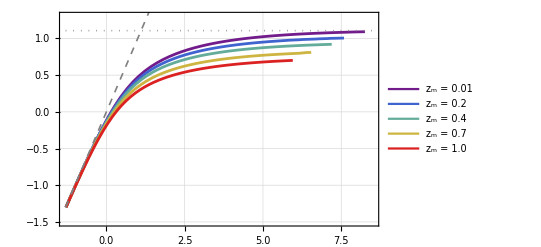

```mathematica
tickLarge = 0.015;
tickSmall = 0.006;
frameTicksSmall = Flatten[Table[{Log10[n 10^i], "", tickSmall}, {n,1,10}, {i, -4, 20, 1}],1];
frameTicksLarge = Table[{Log10[10^i], Superscript[10, i+9], tickLarge}, {i, -4, 20, 1}];
frameTicksLargeDumb = Table[{Log10[10^i], "", tickLarge}, {i, -4, 20, 1}];
frameTicks = Flatten[Join[{frameTicksSmall, frameTicksLarge}],1];
frameTicksDumb = Flatten[Join[{frameTicksSmall, frameTicksLargeDumb}],1];

ghodlaRelationZm = Legended[
  Show[
    {
      plottdKtdC35[#, {ColorData["Rainbow"][#]}] & /@ {0.01, 0.2, 0.4, 0.7, 1.0}, 
      Plot[
        {Log10[timeZ[0]-timeZ[10]], logtdK}, 
        {logtdK, Log10@tdmin0, 50}, 
        PlotStyle->{{Thickness[0.003], Gray, Dotted}, {Thickness[0.003], Gray, Dashed}}
      ]
    },
    PlotRange-> {{Log10@tdmin0, 8.5}, {-1.5, 1.3}},
    FrameTicks ->{{frameTicks, frameTicksDumb}, {frameTicks, frameTicksDumb}}
  ],
  Placed[
    LineLegend[ColorData["Rainbow"][#] & /@ {0.01, 0.2, 0.4, 0.7, 1.0}, 
    Style["z_m = "<>ToString[#], FontFamily->"Times", FontSize -> 15]& /@ {0.01, 0.2, 0.4, 0.70, "1.0"}], 
    {0.8, 0.34}
  ]
]

(*exportOut["ghodlaRelationZm.pdf", ghodlaRelationZm]*)
```

```mathematica
flatSampleSource01 = RandomReal[{minLogtdK35[0.01], maxLogtdK35[.01]}, 10^6];
flatSampleSource5 = RandomReal[{minLogtdK35[0.5], maxLogtdK35[.5]}, 10^6];
flatSampleSource10 = RandomReal[{minLogtdK35[1.0], maxLogtdK35[1.0]}, 10^6];
```

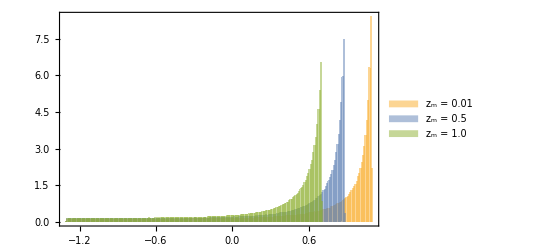

```mathematica
tickLarge = {0, 0.015};
tickSmall = {0, 0.006};
frameTicksSmall = Flatten[Table[{Log10[n 10^i], "", tickSmall}, {n,1,10}, {i, -4, 20, 1}],1];
frameTicksLarge = Table[{Log10[10^i], Superscript[10, i+9], tickLarge}, {i, -4, 20, 1}];
frameTicksLargeDumb = Table[{Log10[10^i], "", tickLarge}, {i, -4, 20, 1}];
frameTicks = Flatten[Join[{frameTicksSmall, frameTicksLarge}],1];
frameTicksDumb = Flatten[Join[{frameTicksSmall, frameTicksLargeDumb}],1];

tdDistributionGhodla = Histogram[
  {
    logtdCCBH35I[.01, #] & /@ flatSampleSource01, 
    logtdCCBH35I[.5, #] & /@ flatSampleSource5,
    logtdCCBH35I[1.0, #] & /@ flatSampleSource10
    (*flatSampleTrue*)
  }, 
  {0.01}, 
  "PDF",
  PlotRange->All, 
  Background->White, 
  Axes -> False, 
  Frame -> True, 
  (*FrameLabel->{"log_10 td", "Counts"}, *)
  FrameStyle-> Directive[Black, 14, FontFamily -> "Times"],
  FrameTicks->{{Automatic, Automatic}, {frameTicks, None}},
  ChartLegends -> Placed[Style["z_m = "<>ToString[#], FontFamily->"Times", FontSize -> 15] & /@ {0.01, 0.5, "1.0"}, {0.2, 0.5}]
  (*ChartStyle-> (ColorData["Rainbow"][#]&) /@ {0.01, 0.6, 1.0}*)
]

(*exportOut["tdDistributionGhodla.pdf", tdDistributionGhodla]*)
```

```mathematica
getAux["tablezTime.mx"]
(*table`zTime = ParallelTable[{t, zTime[t]}, {t, 0.0005 (*z ~ 1000*), 15, 0.0005}]; // EchoTiming*) (*413 seconds*)
(*dumpsave["tablezTime.mx", table`zTime]*)

table`timeZ = {#2, #1} & @@@ table`zTime;
zTimeI = Interpolation[table`zTime];
timeZI = Interpolation[table`timeZ];
```

```mathematica
Clear[flatSampleSource, dataDelayTime];
flatSampleSource[zm_] := flatSampleSource[zm] = RandomReal[{minLogtdK35[zm], maxLogtdK35[zm]}, baseSimPoints];
flatSampleSource4 = flatSampleSource[0.4];
dataDelayTime[zm_] := dataDelayTime[zm] = 10^(logtdCCBH35I[zm, #] & /@ flatSampleSource[zm]);
```

```mathematica
Clear[massFactor, massFactorDelay, dataMassFactor]
massFactor[zm_,zi_] = ((1 + zi)/(1 + zm))^3;

SetAttributes[massFactorDelay, Listable];
massFactorDelay[zm_, td_] =  massFactor[zm, zTimeI[timeZI[zm] - td]];
dataMassFactor[zm_] := dataMassFactor[zm] = massFactorDelay[zm, dataDelayTime[zm]];
```

```mathematica
dataMassFactor[.4]; // EchoTiming
```

116.479

```mathematica
Clear[dataM1Formation, dataM1Merger, 𝒟plp];
𝒟plp = plpp`𝒟[]; (*plpp`𝒟 is defined in PowerLawPlusPeakDefinition.wl.*)
dataM1Merger = RandomVariate[𝒟plp, baseSimPoints] ~ EchoTiming ~ "dataM1Merger"; 

dataM1Formation[zm_]:= dataM1FormationRaw[zm]= dataM1Merger/dataMassFactor[zm];
```

"dataM1Merger"  32.9345

```mathematica
dataM1Formation[0.4]; //EchoTiming
```

0.495725

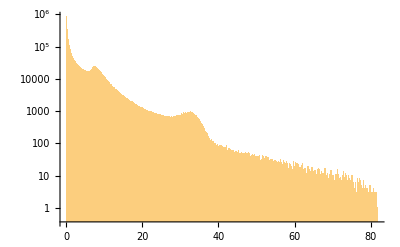

```mathematica
Histogram[dataM1Formation[0.4], {0.05}, "LogCount", PlotRange-> All]
```

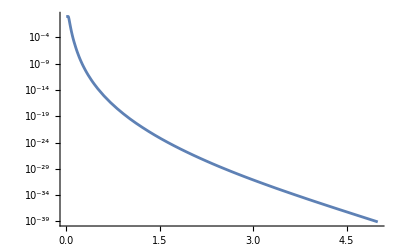

```mathematica
𝒟M1Formation[zm_] := 𝒟M1Formation[zm] = EmpiricalDistribution[dataM1Formation[zm]];
𝒟M1Formation[0.4];
(*LogPlot[SurvivalFunction[𝒟M1Formation[0.4], m1], {m1, 0, 5}]*)
LogPlot[SurvivalFunction[𝒟M1Formation[0.4], m1]^72, {m1, 0, 5}]
```

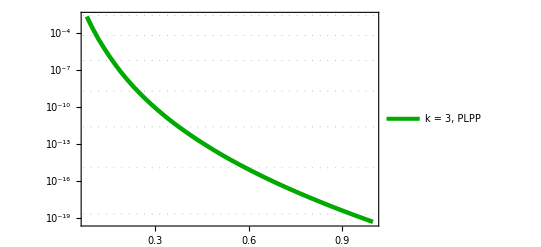

```mathematica
tickLarge = 0.015;
tickSmall = 0.006;
frameTicksSmall = Flatten[Table[{n 10^i, "", tickSmall}, {n,1,10}, {i, -20, 0, 2}],1];
frameTicksLarge = Table[{10^i, Superscript[10, i], tickLarge}, {i, -20, 0, 2}];
frameTicksLargeDumb = Table[{10^i, "", tickLarge}, {i, -4, 0, 1}];
frameTicks = Flatten[Join[{frameTicksSmall, frameTicksLarge}],1];
frameTicksSmallH = Table[{n, "", tickSmall}, {n, 0.0, 1, 0.02}];
frameTicksLargeH = Table[{n, n, tickLarge}, {n, 0.0, 1, 0.1}];
frameTicksH = Flatten[Join[{frameTicksSmallH, frameTicksLargeH}],1];

plotProbabilityNullPLPP = LogPlot[SurvivalFunction[𝒟M1Formation[0.4], m1]^72,
  {m1, 0.08, 1},
  PlotRange->All,
  PlotStyle->{{Thickness[0.008], Darker@Green}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  FrameTicks->{{frameTicksLarge, {probSigma[#], ToString@# <> "σ"} & /@ Range[10]}, {frameTicksH, Automatic}},
  PlotRange->{All, {10^-9,  1}},
  GridLines->{None, probSigma[#]& /@ Range[10]},
  GridLinesStyle->Directive[Gray, Dotted],
  PlotLegends-> Placed[
    {
      Style["k = 3, PLPP", FontFamily->"Times", FontSize -> 14]
    },
    {0.19,0.12}
  ]
]
```

### For the direct method

```mathematica
Clear[dataM1ObsFormation];

mXzDataCentralValues = mXzDataForPlotting1 /. Around[x_, y_] -> x;

dataM1ObsFormation =  (#2 / dataMassFactor[#1]) &  @@@ mXzDataCentralValues; // EchoTiming
```

151.113

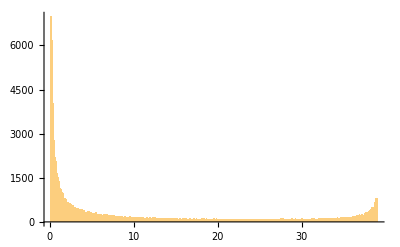

```mathematica
Histogram[dataM1ObsFormation[[10]], {0.1}, PlotRange->All]
```

```mathematica
Clear[𝒟M1ObsFormation];
𝒟M1ObsFormation[event_] := 𝒟M1ObsFormation[event] = EmpiricalDistribution[dataM1ObsFormation[[event]]];
𝒟M1ObsFormation /@ Range[72]; // EchoTiming
```

21.7919

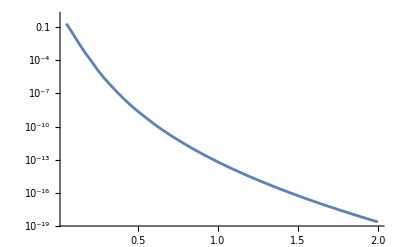

```mathematica
probabiltyNoBHwithMassBelow[m1_] := Product[SurvivalFunction[𝒟M1ObsFormation[event], m1], {event, 1, 72}];

LogPlot[probabiltyNoBHwithMassBelow[m1], {m1, 0.05, 2}]
```

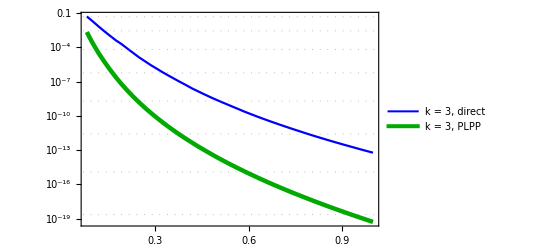

pathOut/plotProbabilityNullGhodla.pdf

```mathematica
plotProbabilityNulldirect = LogPlot[probabiltyNoBHwithMassBelow[m1],
  {m1, 0.08, 1},
  PlotRange->All,
  PlotStyle->{{Thickness[0.004], Blue}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  FrameTicks->{{frameTicksLarge, {probSigma[#], ToString@# <> "σ"} & /@ Range[10]}, {frameTicksH, Automatic}},
  PlotRange->{All, {10^-9,  1}},
  GridLines->{None, probSigma[#]& /@ Range[10]},
  GridLinesStyle->Directive[Gray, Dotted],
  PlotLegends-> Placed[
    {
      Style["k = 3, direct", FontFamily->"Times", FontSize -> 14]
    },
    {0.19,0.22}
  ]
];

plotProbabilityNullGhodla = Show[plotProbabilityNulldirect, plotProbabilityNullPLPP]
exportOut["plotProbabilityNullGhodla.pdf", plotProbabilityNullGhodla]
```

```mathematica
color1i = RGBColor[0, 76/255, 153/255];
color1ii = RGBColor[51/255, 153/255, 255/255];
color1iii = RGBColor[153/255, 0, 0];
color1iv = RGBColor[255/255, 102/255, 102/255];
```

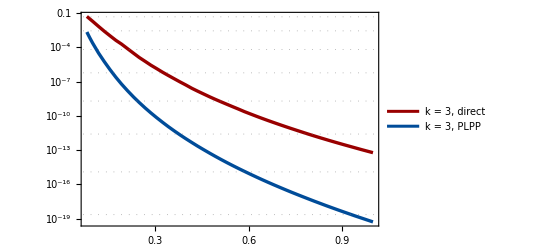

```mathematica
plotProbabilityNullGhodla = -Graphics- /. {Darker@Green -> color1i, Blue -> color1iii, Thickness[0.004] -> Thickness[0.006], Thickness[0.008] -> Thickness[0.006]}
```

```mathematica
exportOut["plotProbabilityNullGhodla.pdf", plotProbabilityNullGhodla]
```

pathOut/plotProbabilityNullGhodla.pdf

## Finding the td distribution for given zi (zFormation) - Not relevant for this work

```mathematica
zTime[t_?NumberQ] := zTime[t, -1];
timeZ[z_?NumberQ] := timeZ[z, -1];

listZtime = ParallelTable[{t, zTime[t]}, {t, timeZ[10], timeZ[-0.9], 0.01}]; (*We only need times from z=10, but we consider mergers for the future as well*)

Clear[zTimeI]
zTimeI[t_?NumberQ] = Interpolation[listZtime][t];
timeMax = listZtime[[-1,1]]; (*Maximum time used to define zTimeI.*)

Clear[tdKerr, tdCCBH];
SetAttributes[tdCCBH, NumericFunction];
SetAttributes[tdKerr, NumericFunction];

tdKerr::usage = "tdKerr[zi, tdC, k] yields the delay time in the auxiliary Kerr picture, 
for a given tdC in the CCBH context with given k. 
zi is the redshift of BBH formation, in the CCBH picture."

tdKerr[zi_?NumberQ, tdC_?NumberQ, k_?NumberQ]:= NIntegrate[
  ((1 + zi)/(1 + zTimeI[t]))^(15 k) , 
  {t, timeZ[zi], tdC + timeZ[zi]},
  PrecisionGoal -> 3,
  AccuracyGoal->Infinity
]; (*For zi = 0, the final time tdC + timeZ[0] will be in the future. Check the limit of zTimeI to see if it is compatible.*)
```

$Aborted

Interpolation::innd: First argument in listZtime does not contain a list of data and coordinates.

Part::partd: Part specification listZtime⟦-1,1⟧ is longer than depth of object.

tdKerr[zi, tdC, k] yields the delay time in the auxiliary Kerr picture, 
for a given tdC in the CCBH context with given k. 
zi is the redshift of BBH formation, in the CCBH picture.

```mathematica
listLogtdKerr3 = ParallelTable[
  {{zi, logtdC}, Log10@tdKerr[zi, 10^logtdC, 3]}, 
  {zi, 0, 10, 0.05}, 
  {logtdC, Log10[tdmin0/2], Log10@timeZ[0] + 0.1, 0.1} (*The maximum is a bit beyond the age of the universe just to include the universe age in the table. *)
] ~ Flatten ~ 1;

listLogtdKerr35 = ParallelTable[
  {{zi, logtdC}, Log10@tdKerr[zi, 10^logtdC, 3/5]}, 
  {zi, 0, 10, 0.05}, 
  {logtdC, Log10[tdmin0/2], Log10@timeZ[0]+ 0.1, 0.1} 
] ~ Flatten ~ 1;

Clear[tdKerr35I, tdKerr3I];
logtdKerr3I = Interpolation[listLogtdKerr3];
logtdKerr35I = Interpolation[listLogtdKerr35];

{minLogtdC, maxLogtdC} = logtdKerr3I["Domain"][[2]]
```

{-1.60206,1.19794}

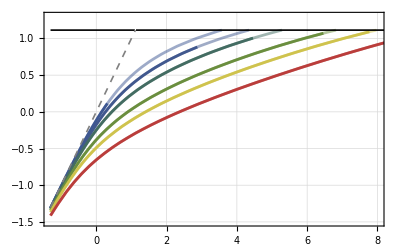

```mathematica
listLogtdCCBH3 = {{#1[[1]], #2}, #1[[2]]} & @@@ listLogtdKerr3 ; (*Generates a table for the inverse function by flipping table entries. *)
listLogtdCCBH35 = {{#1[[1]], #2}, #1[[2]]} & @@@ listLogtdKerr35 ; (*Generates a table for the inverse function by flipping table entries. *)
logtdCCBH3I = Interpolation[listLogtdCCBH3, InterpolationOrder-> 1 (*Required*)];
logtdCCBH35I = Interpolation[listLogtdCCBH35, InterpolationOrder-> 1 (*Required*)];
{minLogtdK[zi_], maxLogtdK[zi_]} := {logtdKerr3I[zi, minLogtdC], logtdKerr3I[zi, maxLogtdC]};
{minLogtdK35[zi_], maxLogtdK35[zi_]} := {logtdKerr35I[zi, minLogtdC], logtdKerr35I[zi, maxLogtdC]};

logtdKz3::usage = "logtdKz3[zi, zObs] provides the log of td in the Kerr frame, 
considering a BBH formed at zi and detected at zObs. Assuming CCBH, the Kerr frame is axiliary, it is not physical.";
logtdKz3[zi_, zObs_] := logtdK /. FindRoot[logtdCCBH3I[zi, logtdK] == Log10[timeZ[zObs] - timeZ[zi]], {logtdK, 1}];
logtdKz35[zi_, zObs_] := logtdK /. FindRoot[logtdCCBH35I[zi, logtdK] == Log10[timeZ[zObs] - timeZ[zi]], {logtdK, 1}];

Clear[plottdKtdC];
plottdKtdC[zi_, style_:Automatic] := Plot[
  logtdCCBH3I[zi, logtdK], 
  {logtdK, Log10@tdmin0, (*maxLogtdCCBH3I[zi]*)maxLogtdK[zi]},
  PlotRange->{All, {-2, Log10[13]}},
  GridLines -> Automatic,
  Frame->True,
  Axes->False,
  Background->White,
  FrameStyle->Directive[Black,14, FontFamily-> "Times"],
  PlotStyle->style
];

plottdKtdC35[zi_, style_:Automatic] := Plot[
  logtdCCBH35I[zi, logtdK], 
  {logtdK, Log10@tdmin0, (*maxLogtdCCBH35I[zi]*)maxLogtdK35[zi]},
  PlotRange->{All, {-2, Log10[13]}},
  GridLines -> Automatic,
  Frame->True,
  Axes->False,
  Background->White,
  FrameStyle->Directive[Black,14, FontFamily-> "Times"],
  PlotStyle->style
];

plottdKtdC35Max[zi_, style_:Automatic] := Plot[
  logtdCCBH35I[zi, logtdK], 
  {logtdK, Log10@tdmin0,  logtdKz35[zi, 0]},
  PlotRange->{All, {-2, Log10[13]}},
  GridLines -> Automatic,
  Frame->True,
  Axes->False,
  Background->White,
  FrameStyle->Directive[Black,14, FontFamily-> "Times"],
  PlotStyle->style
];

(*Show[
  {
    plottdKtdC[#, ColorData["DarkRainbow"][#/10]] & /@ {.1, 2,4, 6, 10},
    plottdKtdC35[#, {Dashed, ColorData["DarkRainbow"][#/10]}] & /@ {.1, 2, 4, 6, 10}, 
    Plot[{Log10@13, If[logtdK < Log10@13, logtdK]}, {logtdK, Log10@tdmin0, 50}, PlotStyle->{{Thickness[0.003], Black}, {Thickness[0.003], Gray}}]
  },
  PlotRange-> {{Log10@tdmin0, 12}, {-1.7, 1.3}}
]*)


tickLarge = 0.015;
tickSmall = 0.006;
frameTicksSmall = Flatten[Table[{Log10[n 10^i], "", tickSmall}, {n,1,10}, {i, -4, 20, 1}],1];
frameTicksLarge = Table[{Log10[10^i], Superscript[10, i+9], tickLarge}, {i, -4, 20, 1}];
frameTicksLargeDumb = Table[{Log10[10^i], "", tickLarge}, {i, -4, 20, 1}];
frameTicks = Flatten[Join[{frameTicksSmall, frameTicksLarge}],1];
frameTicksDumb = Flatten[Join[{frameTicksSmall, frameTicksLargeDumb}],1];

Show[
  {
    plottdKtdC35[#, {Opacity[0.5],ColorData["DarkRainbow"][#/10]}] & /@ {.1, 1, 2, 4, 6, 10},
    plottdKtdC35Max[#, {ColorData["DarkRainbow"][#/10]}] & /@ {.1, 1, 2, 4, 6, 10}, 
    Plot[
      {Log10@13, If[logtdK < Log10@13, logtdK]}, 
      {logtdK, Log10@tdmin0, 50}, 
      PlotStyle->{{Thickness[0.003], Black}, {Thickness[0.003], Gray, Dashed}}
    ]
  },
  PlotRange-> {{Log10@tdmin0, 8}, {-1.5, 1.3}},
  (*FrameLabel->{"log_10 td_Kerr", "log_10td_CCBH"},*)
  FrameTicks ->{{frameTicks, frameTicksDumb}, {frameTicks, frameTicksDumb}}
]
```

Histogram::hbins: The bin specification 0.05 cannot be used to determine either how many or which bins to use.

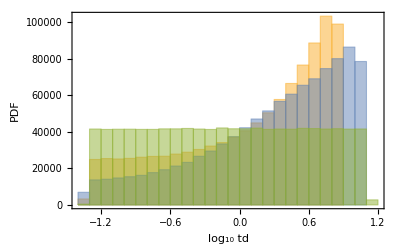

```mathematica
flatSampleSource1 = RandomReal[{Log10@tdmin0, maxLogtdCCBH35I[1]}, 10^6];
flatSampleSource5 = RandomReal[{Log10@tdmin0, maxLogtdCCBH35I[5]}, 10^6];
flatSampleTrue = RandomReal[{Log10@tdmin0, Log10[timeZ[0]-timeZ[10]]}, 10^6];
Histogram[{logtdCCBH35I[1, #] & /@ flatSampleSource1, logtdCCBH35I[5, #] & /@ flatSampleSource5, flatSampleTrue}, 0.05,  PlotRange->All, Background->White, Axes -> False, Frame -> True, FrameLabel->{"log_10 td", "PDF"}, FrameStyle-> Directive[Black, 14, FontFamily -> "Times"]]
```

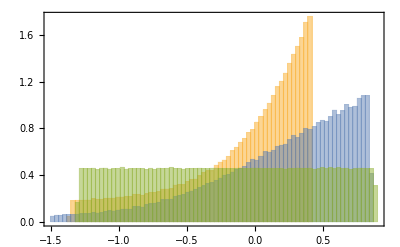

```mathematica
flatSampleSource1 = RandomReal[{Log10@tdmin0, logtdKz3[1,0.5]}, 10^6];
flatSampleSource5 = RandomReal[{Log10@tdmin0, logtdKz3[5,0.5]}, 10^6];
flatSampleTrue = RandomReal[{Log10@tdmin0, Log10[timeZ[0.5]-timeZ[10]]}, 10^6];
Histogram[
  {
    logtdCCBH3I[1, #] & /@ flatSampleSource1, 
    logtdCCBH3I[5, #] & /@ flatSampleSource5, 
    flatSampleTrue
  }, 
  {0.03},
  "PDF", 
  PlotRange->All, 
  Background->White, 
  Axes -> False, 
  Frame -> True, 
  (*FrameLabel->{"log_10 td", "Counts"}, *)
  FrameStyle-> Directive[Black, 14, 
  FontFamily -> "Times"]
]
```